```mathematica
n=3;
(p=Random[]&/@Range[n];
p=p/Total[p];
q=Random[]&/@Range[n];
q=q/Total[q];
Total[p*p]-Total[p*q])&/@Range[100]
```

{-0.00241276,0.021111,0.064693,0.209165,0.0480403,0.214685,0.0330964,0.0445269,0.0457089,-0.0401423,0.0311149,0.02195,0.0519884,0.142134,0.00090807,0.428799,0.0271062,0.253954,0.0281097,0.00803448,0.00675756,0.0502639,0.0311013,0.0637589,-0.0261328,0.00392722,0.340772,0.123628,0.0614746,0.459804,0.0460263,0.0042238,0.289968,0.115116,0.0560068,0.349003,0.226734,0.0974664,0.0460646,0.0757058,0.118218,0.518708,0.0439675,0.0952143,0.30982,-0.136926,0.0962804,0.0280659,0.148661,0.0187718,0.000298749,0.107402,0.137445,0.0610386,0.0216653,0.0978306,0.144409,0.161285,-0.0518192,0.472033,0.0709458,0.0861803,0.203051,-0.0328274,0.105636,-0.0353381,0.235849,0.062026,0.0202906,0.824676,0.00023815,0.389611,-0.0207484,0.266365,0.0837081,0.000589498,0.0711834,0.168335,-0.00739527,0.0472567,0.119533,0.0751337,0.100494,0.0812423,0.149657,0.125225,0.0725203,0.242049,0.173296,0.00832303,0.0390753,0.0262806,0.0713437,0.105973,-0.00378967,0.154871,0.00877784,0.145609,-0.013262,-0.0143355}

```mathematica
p
```

{0.265942,0.281848,0.45221}

```mathematica
q
```

{0.190261,0.280448,0.529291}

```mathematica
p={3/4,1/8,1/8};
q={2/3,1/6,1/6};
p.p//N
p.q//N
q.q//N
```

0.59375

0.541667

0.5

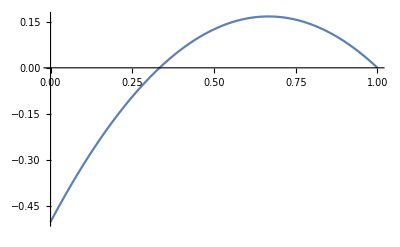

```mathematica
Plot[{q-(q^2+(1-q)^2/2)},{q,0,1}]
```

```mathematica
Total[p*q]
Total[p*p]
```

0.368993

0.354657

```mathematica
Solve[pp^2+(1-pp)^2==pp qq + (1-pp)(1-qq),qq]
```

{{qq→pp}}

```mathematica
Min@%
```

0.00176594

```mathematica
any=False;
n=3;
nn=10000;
(probs=Table[Random[],{i,1,n},{j,1,n}];
probs=probs/Total[Total[probs]];
phs=Total[probs];
pes=Total/@probs;
conds=probs/pes;
eph=phs.phs;
ephe=Total[Total[conds*probs]];
any=Or[any,ephe<eph];)&/@Range[nn];
any
```

False

```mathematica
probs={{a,b,c},{d,e,f},{g,h,i}};
Total[Total[probs]]
probs=probs/Total[Total[probs]];
phs=Total[probs];
pes=Total/@probs;
conds=probs/pes;
eph=phs.phs;
ephe=Total[Total[conds*probs]];
(ephe-eph//Simplify)/.{a+b+c+d+e+f+g+h+i->1}//Simplify
```

a+b+c+d+e+f+g+h+i

a^2/(a+b+c)+b^2/(a+b+c)+c^2/(a+b+c)+d^2/(d+e+f)+e^2/(d+e+f)+f^2/(d+e+f)-(a+d+g)^2-(b+e+h)^2-(c+f+i)^2+g^2/(g+h+i)+h^2/(g+h+i)+i^2/(g+h+i)

```mathematica
NMinimize
```

NMinimize[f,x] minimizes f numerically with respect to x.
NMinimize[f,{x,y,…}] minimizes f numerically with respect to x, y, …. 
NMinimize[{f,cons},{x,y,…}] minimizes f numerically subject to the constraints cons. 
NMinimize[…,x∈reg] constrains x to be in the region reg.

```mathematica
Fold[And,(.001<=#≤.999)&/@{a,b,c,d,e,f,g,h,i}]
```

0.001≤a≤0.999&&0.001≤b≤0.999&&0.001≤c≤0.999&&0.001≤d≤0.999&&0.001≤e≤0.999&&0.001≤f≤0.999&&0.001≤g≤0.999&&0.001≤h≤0.999&&0.001≤i≤0.999

```mathematica
NMinimize[{a^2/(a+b+c)+b^2/(a+b+c)+c^2/(a+b+c)+d^2/(d+e+f)+e^2/(d+e+f)+f^2/(d+e+f)-(a+d+g)^2-(b+e+h)^2-(c+f+i)^2+g^2/(g+h+i)+h^2/(g+h+i)+i^2/(g+h+i),a+b+c+d+e+f+g+h+i==1&&(0.001≤a≤0.999&&0.001≤b≤0.999&&0.001≤c≤0.999&&0.001≤d≤0.999&&0.001≤e≤0.999&&0.001≤f≤0.999&&0.001≤g≤0.999&&0.001≤h≤0.999&&0.001≤i≤0.999)
},{a,b,c,d,e,f,g,h,i}]
```

{1.99493×10^-16,{a→0.0866175,b→0.0856416,c→0.0347031,d→0.144499,e→0.142871,f→0.0578933,g→0.187402,h→0.18529,i→0.0750821}}

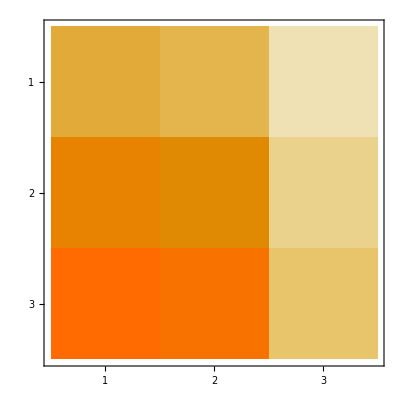

```mathematica
(probs/.%561[[2]])//MatrixPlot
```

```mathematica
probs/.%461[[2]]
```

{{-0.0367285,0.0350625,1.50754×10^-6},{0.0208378,0.202632,1.84474×10^-6},{0.255317,0.304439,0.218437}}

```mathematica
{z
```

```mathematica
probs/phs
```

{{0.128981,0.311688,0.265064},{0.459225,0.505106,0.57442},{0.340667,0.128751,0.354796}}

```mathematica
probs[[1]]/phs[[1]]
```

{0.128981,0.311688,0.265064}

```mathematica
mat={{1,2,3},{0,0,0},{1,0,0}}
mat.mat
mat*mat
```

{{1,2,3},{0,0,0},{1,0,0}}

{{4,2,3},{0,0,0},{1,2,3}}

{{1,4,9},{0,0,0},{1,0,0}}